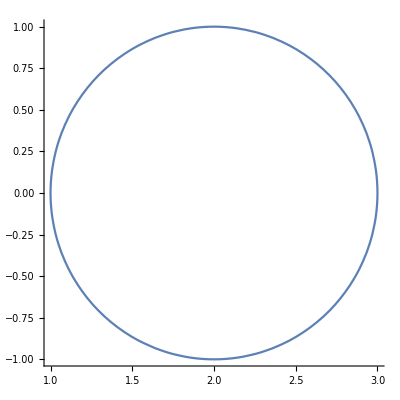

```mathematica
p=ContourPlot[(x-2)^2+y^2==1,{x,1,3},{y,-1,1},Axes->True,Frame->False,AxesOrigin->{0,0},PlotRange->All,AspectRatio->Automatic,Exclusions->{x≤2||y<=0},ExclusionsStyle->Dashed]
```

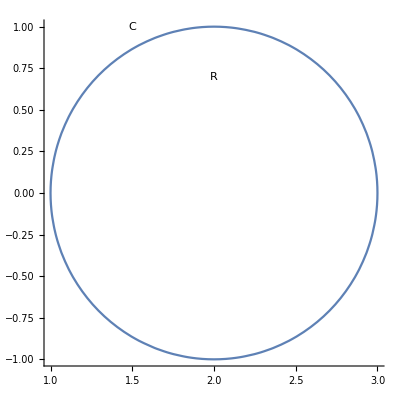

```mathematica
Show[p,Graphics[{Text[C,{1.5,1}],Text[R,{2,0.7}]}]]
```

```mathematica
PlotStyle
```

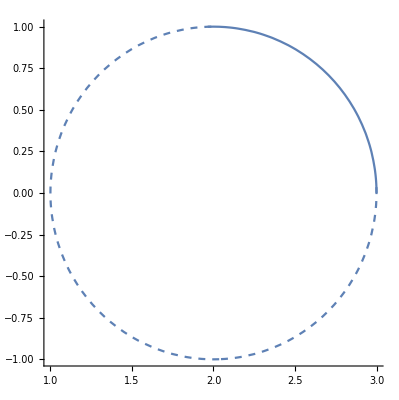

```mathematica
p1=ContourPlot[(x-2)^2+y^2==1,{x,1,3},{y,-1,1},RegionFunction->(#2≤0||#1≤2&),ContourStyle->Dashed];
p2=ContourPlot[(x-2)^2+y^2==1,{x,1,3},{y,-1,1},RegionFunction->(#2>0&&2≤#1≤3&)];
Show[{p1,p2},Axes->True,Frame->False,AxesOrigin->{0,0},PlotRange->All,AspectRatio->Automatic]
```

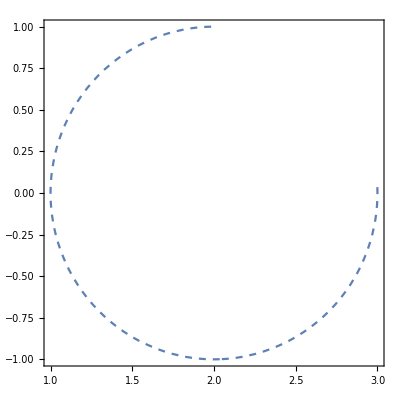

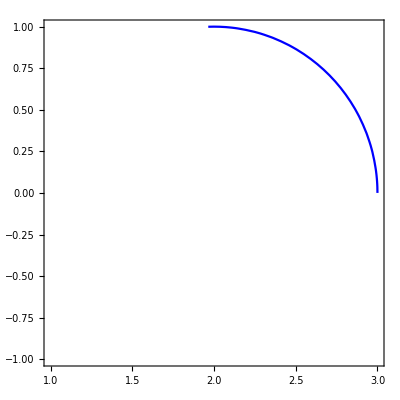

```mathematica
p1
p2
```